## Code Archived

```mathematica
(* 
harmonicAnalysis[a_,b_,c_,d_]:=Block[{p=a,q=b,r=c,s=d,coeff,θ,rotationMat,starMat,ψ,L,W,ϕ},
θ = 0.5ArcTan[(p^2  +r^2 -q^2-s^2),2(p q + r s)];
coeff = {p,q,r,s};
rotationMat = {{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}};
starMat=Partition[coeff,2,2].rotationMat;
ψ=ArcTan[starMat[[1,1]],starMat[[2,1]]]*(180 /Pi);
ϕ=ArcTan[starMat[[1,2]],starMat[[2,2]]]*(180 /Pi);
L = Norm[{starMat[[1,1]],starMat[[2,1]]}];
W= Norm[{starMat[[1,2]],starMat[[2,2]]}];
{L,W,ψ,ϕ}];
 *)
```

```mathematica
(*
ClearAll@EllipticalFourier;
Options[EllipticalFourier] = {normalize-> True,sizeInvariance-> True,order-> 10,ptsToplot-> 300,locus-> {0.,0.},areathreshold-> 2};
EllipticalFourier[mask_,OptionsPattern[]]:=Module[{dXY,dt,t,T,ϕ,contourpositions, contour,contourtour,contourregion,xi,A0,δ,C0,dCval,coeffL,normalizeEFD,ellipticalCoefficients,plotEFD},
contourpositions = PixelValuePositions[MorphologicalPerimeter[mask],1];
contourtour=Last@FindShortestTour[contourpositions];
contour = Part[contourpositions,contourtour];
contourregion=BoundaryMeshRegion[contourpositions,Line@contourtour];
dXY = Differences[contour];
dt=(x↦N@Sqrt[x])[Total/@(dXY^2)];
t = Prepend[Accumulate[dt],0];
T= Last@t;
ϕ = 2 π t/T;

normalizeEFD[coeff_]:= With[
{θ=0.5 ArcTan[(coeff[[1,1]]^2 -coeff[[1,2]]^2 + coeff[[1,3]]^2 -coeff[[1,4]]^2),
2 (coeff[[1,1]] coeff[[1,2]] +coeff[[1,3]] coeff[[1,4]])]},
Block[{coeffList = coeff,ψ,ψr,a,c,θr},
θr[i_Integer]:={{Cos[i θ],-Sin[i θ]},{Sin[i θ],Cos[i θ]}};
coeffList=Partition[#,2,2]&/@coeffList;
coeffList=MapIndexed[(#1.θr[First@#2])&,coeffList];
a=First@Flatten@First@coeffList;
c=(Flatten@First@coeffList)[[3]];
ψ = ArcTan[a,c];
ψr= {{Cos[ψ],Sin[ψ]},{-Sin[ψ],Cos[ψ]}};
coeffList=MapIndexed[Flatten[ψr.#]&,coeffList];
If[OptionValue[sizeInvariance],a= First@First@coeffList;coeffList/=a,coeffList]]
];

ellipticalCoefficients[order_]:= Module[{coeffs,func},
func[list:{{__}..},n_Integer]:=Block[{listtemp =list, const = T/(2 (n^2)( π^2)),phiN= ϕ *n,
dCosPhiN, dSinPhiN,an,bn,cn,dn},
dCosPhiN = Cos[Rest@phiN]-Cos[Most@phiN];
dSinPhiN = Sin[Rest@phiN]-Sin[Most@phiN];
an = const*Total@(dXY[[All,1]]/dt *dCosPhiN);
bn = const*Total@(dXY[[All,1]]/dt*dSinPhiN);
cn = const*Total@(dXY[[All,2]]/dt*dCosPhiN);
dn = const*Total@(dXY[[All,2]]/dt*dSinPhiN);
listtemp[[n]]= {an,bn,cn,dn};
listtemp
];
coeffs = ConstantArray[0,{order,4}];
coeffL= If[OptionValue@normalize,normalizeEFD[#],#]&@Fold[func,coeffs,Range@order]
];

dcCoefficients:=(
xi =  Accumulate[Part[dXY,All,1]]- (dXY[[All,1]]/dt)*Rest@t;
A0= (1/T)*Total@(dXY[[All,1]]/(2 dt) * Differences[t^2] +  xi*dt);
δ = Accumulate[Part[dXY,All,2]]- (dXY[[All,2]]/dt)*Rest@t;
C0= (1/T)*Total@(dXY[[All,2]]/(2 dt) * Differences[t^2] +  δ*dt);
{First@First@contour + A0,Last@First@contour+C0}
);

plotEFD[coeff_]:= Last@Reap@Block[{n = Length@coeff,nhalf,nrow=2,ti,xt,yt,func,θ,
i=OptionValue[ptsToplot],j,regionpts,shortesttour,regiondiff,regiondiffmetric},
nhalf = Ceiling[n/2];
ti = Array[#&,i,{0.,1}];
xt = ConstantArray[OptionValue[locus][[1]],i];
yt = ConstantArray[OptionValue[locus][[2]],i];
regiondiffmetric =100;
j=1;
While[regiondiffmetric>OptionValue[areathreshold],
xt+= coeff[[j,1]] Cos[2 (j) π ti] + coeff[[j,2]] Sin[2 (j) π ti];
yt += coeff[[j,3]]Cos[2(j) π ti] + coeff[[j,4]] Sin[2 (j)π ti];

regionpts=Most@Thread@{xt,yt};
shortesttour = Line@Last@FindShortestTour@regionpts;
regiondiff=BoundaryMeshRegion[regionpts,shortesttour]~RegionDifference~contourregion;
regiondiffmetric = Area[regiondiff]/Area[contourregion] * 100;
Sow@{harmonicAnalysis[Sequence@@coeff[[j]]],Graphics[{{Thick,XYZColor[0,0,1,0.6],Line@Thread[{xt,yt}]},{Thick,Dashed,XYZColor[1,0,0,0.6],Line@contour},Inset[Style[#,{Black,FontSize->12}]&@Text["harmonic: " <> ToString@j]]}]};
j++
] ;
];
ellipticalCoefficients[OptionValue[order]];
plotEFD[coeffL]
];
*)
```

```mathematica
(* ClearAll[plotElongCont];
Options[plotElongCont]={"contrast" -> "normalized","join"-> True,"filter"-> 5,
"filling"-> {1->{{2},{LightGreen,LightBlue}}},"imgsize"-> 200,"rescale"-> True};
plotElongCont[res_,harmonics_,OptionsPattern[]] :=With[{secondharmonic=harmonics,size=OptionValue["imgsize"],
rad=OptionValue["filter"],j=OptionValue["join"],fill=OptionValue["filling"]},
 Module[{contrast, radratio, g, ind1, 
len = Replace[res,{p:{HoldPattern[_-> _]..}:> Length@{p},x_ :> Length[x]}], results = res},
If[len==1, results = {res}];
ind1 = Switch[OptionValue["contrast"],"normalized", -2, _ , -1];
Function[x,
(contrast = Max /@ ((Values /@ results[[x]])[[All, ind1]]);
If[OptionValue["rescale"],
Show[
ListPlot[{Thread[{If[#==1, 72, N[#/6+72,4]]&/@Keys@results[[x]], #}]&[GaussianFilter[Rescale@contrast,rad]],
Thread[{Part[secondharmonic[[x]],All,1],GaussianFilter[Rescale@secondharmonic[[x]][[All,2]],rad]}]} ,
 Joined ->j,PlotStyle -> {{Thick,RGBColor[0.07924700513978256, 0.07394564469935314, 0.4499539624003866]},{Thick,RGBColor[0.10823426242933962, 0.6204150625738422, 0.4678154145759483]}},Filling->fill,PlotRange->{{72,92},{0.,1.}},ImageSize->size,PlotLegends-> {"polarization","tip elongation"},AxesLabel->{"hrs pp",""}],
Graphics[{Opacity[0.5],Dashed,Thick,Black,Line[{{82.5,0.0},{82.5,1.0}}]}]
],
{ListPlot[Thread[{If[#==1, 72, N[#/6+72,4]]&/@Keys@results[[x]], #}]&[GaussianFilter[contrast,rad]],Joined->True,
PlotStyle->{Thick,RGBColor[0.07924700513978256, 0.07394564469935314, 0.4499539624003866]},AxesStyle->Directive[Black,Bold,12],AxesLabel->{"hrs pp","polarization"},Filling->Axis,
PlotRange->{{72,92},{0,Automatic}}],
ListPlot[Thread[{Part[secondharmonic[[x]],All,1],GaussianFilter[secondharmonic[[x]][[All,2]],rad]}],Joined->True,
PlotStyle->{Thick,RGBColor[0.10823426242933962, 0.6204150625738422, 0.4678154145759483]},AxesStyle->Directive[Black,Bold,12],AxesLabel->{"hrs pp","elongation"},Filling->Axis,
PlotRange->{{72,92},{0,Automatic}}]}
])
]/@Range[Length@res]
]
]
*)
```

## Initialize

```mathematica
<<"C:\\Users\\aliha\\Desktop\\analysis notebooks\\polarization-elongation\\Current\\Pol-Elong.m";
<<"C:\\Users\\aliha\\Desktop\\analysis notebooks\\polarization-elongation\\Current\\EFD.m";
```

```mathematica
numImages=120;
```

```mathematica
dir="C:\\Users\\aliha\\Desktop\\research related\\raw data\\@polarization prior elongation\\New\\30\\mask 30\\";
```

```mathematica
maskfnames = Import[dir];
ordering=Ordering@Flatten@StringCases[maskfnames,x:DigitCharacter..:> FromDigits[x]];
maskfnames=maskfnames[[ordering]];
masks=Import[dir<>#]&/@maskfnames;
```

```mathematica
Through[{First,Last}[masks]]
```

{-Graphics-,-Graphics-}

```mathematica
result=EllipticalFourier[#,normalize-> False,order->10,ptsToplot-> 200,locus-> "dcCoefficients"]&/@masks;
```

```mathematica
(* convert to dataset *)
```

```mathematica
results=result/._Graphics-> Sequence[];
results=Map[Flatten[#,1]&]@(results/.{x___Real}:> x);
```

```mathematica
Length@results
```

96

```mathematica
savedmod=Thread[Sort@Flatten@StringCases[maskfnames,x:DigitCharacter..:> FromDigits[x]]->results];
```

```mathematica
dataset=Dataset@*Association@MapAt[<|"L"->#[[1]],"W"->#[[2]],"ψ"->#[[3]],"θ"->#[[4]]|>&/@#&,savedmod,{All,2}];
```

```mathematica
Clear@func;
func[x_,y_,z_]:=Thread[{Keys@#,Values@#}]&@Normal@x[[All,y,z]]//DeleteCases[#,{_,Missing[__]}]&//Sort;
```

```mathematica
mag=Block[{subset,lengthfirst,widthfirst,lengthsecond,widthsecond,lengththird,widththird},
Transpose@Map[(
subset=dataset[[#]];
lengthfirst=func[subset,1,"L"];
widthfirst=func[subset,1,"W"];
lengthsecond=func[subset,2,"L"];
widthsecond=func[subset,2,"W"];
lengththird=func[subset,3,"L"];
widththird=func[subset,3,"W"];
{lengthfirst,widthfirst,lengthsecond,widthsecond,lengththird,widththird})&,{Range@Length@dataset}]
];
```

```mathematica
interval=6;startPeriod=72;endperiod=92;
```

```mathematica
mag= N@MapAt[#/interval+startPeriod&,mag,{All,All,All,1}];
```

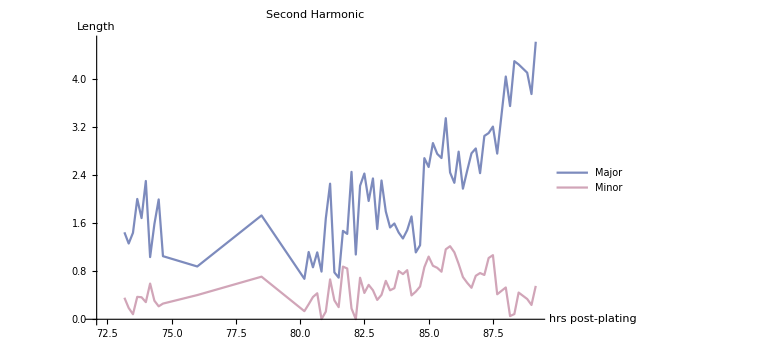

```mathematica
ListPlot[{Sort@Flatten[mag[[3]],1],Sort@Flatten[mag[[4]],1]},PlotStyle->{Lighter@RGBColor[0.23662366005378166, 0.3201359349257917, 0.6098683946554636],RGBColor[0.8198505325329045, 0.6456033728674139, 0.7200310784497016]},Joined->True,AxesLabel->{"hrs post-plating","Length"},LabelStyle->Directive[{Black,14}],PlotLegends->{"Major","Minor"},PlotLabel->"Second Harmonic",PlotRange->{{startPeriod,All},Automatic}, ImageSize->Large]
```

```mathematica
secondharmonic=With[{lenindices=3},
Thread[{Flatten[mag[[#]],1][[All,1]],Flatten[mag[[#]],1][[All,2]]*Flatten[mag[[#+1]],1][[All,2]]}]&[lenindices]
];
```

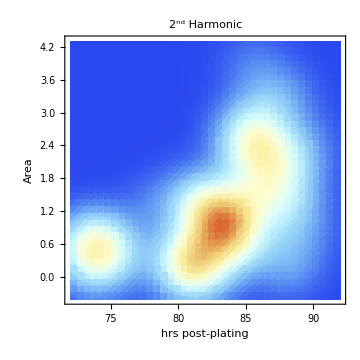

```mathematica
With[{lenindices={3}},
MapThread[
SmoothDensityHistogram[#,ColorFunction->"LightTemperatureMap",MeshStyle->{Dashed,Thick,Black},Mesh->3,
FrameLabel->{Style[#,Black,FontSize->14]&@"hrs post-plating",Style[#,Black,FontSize->14]&@"Area"},
PlotLabel->Style[#2,FontSize->15],FrameTicksStyle->14,PlotRange-> {{startPeriod,endperiod},Automatic},
ImageSize->Medium,AspectRatio->1]&,
{Thread[{Flatten[mag[[#]],1][[All,1]],Flatten[mag[[#]],1][[All,2]]*Flatten[mag[[#+1]],1][[All,2]]}]&/@lenindices,
{"2^nd Harmonic"}}
]
]
```

```mathematica
Options[contrastTheta]={"imageSize"->{160,160}}; 
saved=contrastElong["C:\\Users\\aliha\\Desktop\\research related\\raw data\\@polarization prior elongation\\New\\","mask ","signal"][#]&/@{30}
```

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

83

84

85

86

87

88

89

90

91

92

93

94

96

97

98

99

101

102

103

{{5→{260,3318.25,0.0615939,{60.7618,66.2258},{29.6852,33.4936},{0.00610065,0.112982},{8.5715,158.217}},6→{256,3184.,0.0809734,{59.077,65.226},{28.6804,32.9859},{0.0037527,0.125837},{4.8975,162.876}},7→{262,3254.88,0.0493434,{60.425,65.4438},{29.3912,34.1658},{0.00529543,0.129717},{6.87869,169.977}},8→{266,3354.88,0.0787099,{61.2885,67.7997},{29.0833,34.7805},{0.0170545,0.112337},{25.0365,163.073}},9→{274,3462.63,0.0950254,{61.8249,70.1145},{29.7439,36.1428},{0.0021214,0.135945},{3.00784,187.891}},10→{268,3280.5,0.0567144,{60.6402,66.5608},{28.9284,34.6463},{0.0127352,0.144105},{15.4169,176.004}},11→{274,3584.13,0.110892,{62.7559,71.1393},{30.2654,36.8438},{0.00938401,0.137997},{13.9538,203.257}},12→{276,3512.5,0.117134,{61.6036,70.9812},{29.5148,36.556},{0.00292601,0.167425},{3.69529,208.885}},13→{282,3692.,0.118912,{63.0367,74.1076},{30.1232,37.571},{0.00159697,0.137515},{2.43476,205.212}},14→{276,3636.5,0.08816,{63.3225,71.2168},{30.4495,36.4598},{0.00896783,0.153411},{12.083,202.909}},15→{276,3663.88,0.0899568,{62.6355,70.5283},{30.7983,36.522},{0.00120724,0.129943},{1.73622,183.146}},16→{268,3575.,0.113109,{61.0168,70.962},{30.1387,36.8883},{0.00487485,0.136234},{6.65802,186.296}},17→{268,3567.88,0.13903,{60.2575,71.4366},{29.3868,36.8895},{0.0019322,0.145223},{2.6959,202.272}},18→{268,3585.75,0.134213,{60.9944,71.9318},{29.2611,36.8437},{0.00814363,0.148775},{11.1005,203.223}},19→{276,3754.5,0.0794752,{64.4273,71.0458},{31.1617,36.5326},{0.00877497,0.152581},{12.3576,217.449}},20→{278,3810.38,0.0873424,{63.8422,71.3729},{31.4929,36.4835},{0.00142112,0.141185},{2.17861,218.616}},21→{282,3831.25,0.0990517,{65.1566,73.0117},{31.1521,37.4312},{0.00244791,0.153043},{3.58499,223.161}},22→{282,3862.,0.102046,{64.6365,73.1427},{31.4337,37.1693},{0.00523958,0.137234},{8.09026,211.761}},23→{292,3993.75,0.118667,{65.8386,75.2129},{31.904,38.6961},{0.00144847,0.104401},{2.62133,189.786}},24→{290,4030.5,0.117606,{66.1019,76.1173},{31.5486,39.1893},{0.00135295,0.137654},{1.95625,199.204}},25→{282,3910.75,0.0623752,{66.1699,72.4494},{32.0579,37.4665},{0.00650062,0.134711},{10.0277,207.583}},26→{282,3954.75,0.0746794,{65.8054,72.8913},{32.312,36.9865},{0.00894023,0.125342},{14.5285,197.9}},27→{284,3971.88,0.0839267,{65.2685,73.2223},{31.6964,36.9195},{0.00624733,0.118147},{10.6151,200.406}},28→{288,4043.63,0.075999,{66.491,73.9501},{32.7127,37.6749},{0.0031124,0.117036},{5.57244,209.069}},29→{290,4079.75,0.0723055,{67.559,74.1687},{33.6425,38.0903},{0.00541458,0.133336},{8.58799,213.622}},30→{290,3992.,0.0448293,{67.5589,72.3564},{33.1085,37.0719},{0.00376244,0.137325},{6.46415,235.25}},31→{290,4054.5,0.0226878,{69.0582,73.2391},{33.5504,37.5475},{0.000381254,0.130861},{0.673472,230.723}},32→{288,4068.38,0.028087,{68.9396,72.674},{32.9361,36.6532},{0.00740746,0.129375},{12.3014,213.566}},33→{290,4108.38,0.0236,{68.9231,72.6377},{33.6438,36.8169},{0.000415127,0.137785},{0.747677,249.212}},34→{292,4181.38,0.0418102,{69.2684,73.869},{34.3391,37.7062},{0.00163748,0.132611},{3.05223,247.196}},35→{294,4212.38,0.0477202,{69.7578,74.027},{34.1652,38.0324},{0.0110818,0.132314},{21.4198,250.167}},36→{302,4365.13,0.0529434,{70.8977,76.2129},{34.7375,38.9724},{0.00558706,0.134907},{11.13,269.841}},37→{302,4371.25,0.0367182,{70.9171,76.2053},{34.9531,38.9759},{0.00407499,0.12995},{8.46282,266.879}},38→{306,4494.5,0.0529151,{71.3735,76.5676},{33.9812,38.5152},{0.0106784,0.122122},{21.1651,240.198}},39→{310,4548.88,0.0300123,{71.545,77.0036},{35.3021,39.1139},{0.00631037,0.140789},{12.5481,281.025}},40→{306,4495.25,0.0746148,{70.3687,79.3599},{34.1571,40.2087},{0.00703674,0.139021},{14.7704,288.43}},41→{298,4411.13,0.0867521,{70.0862,78.7598},{33.9508,39.904},{0.00994732,0.161908},{19.7303,319.014}},42→{300,4468.38,0.0596062,{71.13,77.461},{35.1983,39.8524},{0.00509194,0.171562},{9.44538,317.15}},43→{298,4356.5,0.00578833,{71.2045,74.5198},{34.7266,38.1615},{0.000797724,0.170878},{1.47509,315.069}},44→{300,4391.63,0.0258159,{71.6613,74.7241},{35.355,38.8098},{0.0116284,0.163035},{21.2861,297.705}},45→{304,4597.63,0.0748659,{71.0975,79.1052},{35.4009,40.4339},{0.00439774,0.179065},{8.77582,356.497}},46→{310,4695.,0.040377,{73.8675,78.563},{36.3369,39.682},{0.0123335,0.147771},{24.385,290.554}},47→{316,4679.25,0.0281959,{73.1168,79.0343},{35.738,39.6914},{0.00230538,0.146895},{4.70614,295.074}},49→{322,4758.25,0.0687164,{71.637,81.979},{34.8075,41.3183},{0.0117068,0.145869},{23.4598,289.938}},50→{322,4820.88,0.105209,{72.7187,82.3608},{35.106,42.0415},{0.00616254,0.146638},{13.1411,307.722}},51→{314,4707.38,0.113916,{70.6638,82.314},{34.0244,41.8555},{0.00237876,0.161292},{4.65562,309.564}},52→{312,4654.38,0.131389,{69.5421,82.5679},{33.2309,42.5624},{0.00466907,0.142135},{8.66296,263.336}},53→{308,4527.38,0.0949234,{69.0757,80.2299},{33.4058,40.5501},{0.00579407,0.145964},{11.1743,279.177}},54→{312,4547.13,0.065662,{70.1475,78.3685},{33.8149,39.7142},{0.00257857,0.164997},{4.37052,277.565}},55→{318,4786.25,0.0655495,{72.8494,81.3678},{33.943,41.7207},{0.00817157,0.173666},{14.9235,319.291}},56→{328,5017.,0.068233,{73.6221,83.3515},{35.4382,41.813},{0.00179504,0.172617},{3.58376,343.213}},57→{334,5064.5,0.0893778,{73.2385,85.5462},{35.3925,42.8464},{0.00542793,0.173238},{10.4263,331.044}},58→{332,5047.38,0.0390832,{75.9419,83.23},{35.1599,42.4041},{0.0141873,0.18686},{27.7427,358.012}},59→{334,5124.38,0.0452217,{75.8561,83.807},{36.3083,42.745},{0.0043919,0.156675},{9.06336,320.423}},60→{328,5092.63,0.0615265,{75.3197,83.9988},{35.1039,42.7243},{0.0017645,0.168643},{3.6858,349.117}},61→{334,5177.5,0.0703981,{75.7212,86.0959},{36.5376,43.1947},{0.011154,0.180682},{22.1134,357.514}},62→{334,5097.25,0.041515,{76.2463,82.2802},{35.9557,42.6066},{0.00137286,0.176716},{2.73316,346.424}},63→{330,5081.63,0.0437634,{75.1974,82.4184},{34.981,43.0446},{0.0150339,0.194647},{29.3954,377.378}},64→{334,5141.88,0.103088,{75.4967,85.9344},{35.878,44.2324},{0.00124136,0.196081},{2.64556,413.502}},65→{326,5107.75,0.120396,{74.7478,85.276},{35.855,43.2664},{0.00723144,0.19444},{14.7074,387.725}},66→{328,5111.25,0.135642,{74.007,87.004},{35.4589,44.2817},{0.0103103,0.195427},{20.7461,391.45}},67→{338,5217.25,0.121955,{74.2585,87.5218},{35.76,45.2786},{0.0031952,0.184524},{6.87857,396.982}},68→{342,5378.75,0.115371,{75.1834,89.6297},{35.8691,45.4311},{0.00851172,0.171816},{18.9606,376.884}},69→{340,5458.88,0.113726,{75.9871,90.2001},{36.903,45.4968},{0.00133201,0.184117},{2.761,380.776}},70→{348,5567.88,0.123018,{75.3026,89.939},{36.6233,46.6753},{0.0109821,0.199374},{23.019,411.521}},71→{348,5578.63,0.11855,{76.6411,90.8311},{36.2331,46.2991},{0.00292561,0.190481},{6.61379,425.096}},72→{346,5549.63,0.116007,{76.2041,89.5801},{36.8359,45.7456},{0.0101611,0.168741},{24.903,408.967}},73→{354,5593.63,0.0996685,{77.6591,91.1227},{37.1257,46.8996},{0.00141589,0.181618},{3.30526,424.105}},74→{362,5672.63,0.129911,{76.9311,94.2014},{37.2943,47.8675},{0.0162912,0.183093},{35.5959,399.982}},75→{360,5732.25,0.146291,{77.1507,94.914},{37.2337,48.0074},{0.00369341,0.190123},{8.57778,439.864}},76→{358,5648.63,0.12714,{76.8625,92.5085},{36.6123,46.8763},{0.000465976,0.217974},{0.983047,459.7}},77→{360,5767.75,0.134926,{75.6121,92.9439},{35.4523,48.6222},{0.0159233,0.223226},{33.8305,469.351}},78→{358,5815.,0.130626,{77.6581,92.1878},{36.5078,49.0319},{0.0230694,0.219383},{50.6909,476.946}},79→{364,5881.38,0.130966,{77.1443,92.3902},{36.5598,48.3679},{0.00721859,0.214667},{17.0422,505.263}},80→{366,5832.63,0.130154,{78.6459,92.2501},{37.3583,48.5447},{0.00223535,0.22405},{5.26,523.014}},81→{366,5873.75,0.125841,{78.6681,93.1268},{37.08,48.843},{0.0133939,0.195062},{34.0034,495.271}},82→{370,5979.38,0.121198,{77.9998,92.9724},{36.3855,49.2929},{0.0103538,0.224671},{24.6064,530.786}},83→{372,5991.,0.107017,{78.7982,92.9055},{36.9987,48.6908},{0.00779965,0.201545},{19.5856,504.388}},84→{360,6072.5,0.103875,{79.2737,92.8001},{36.7832,49.1753},{0.00134345,0.203801},{3.37554,510.601}},85→{362,5974.25,0.114558,{78.1301,93.7338},{36.1295,49.2222},{0.0104852,0.224347},{25.6746,547.387}},86→{360,6024.5,0.129221,{79.2268,94.1937},{36.8167,48.521},{0.00307262,0.230945},{7.55245,565.549}},87→{358,5926.88,0.122418,{77.8964,94.0597},{36.2431,48.451},{0.0116346,0.207341},{28.2634,504.396}},88→{360,6067.38,0.151551,{78.0591,95.2739},{36.4689,49.0256},{0.0128686,0.23808},{32.0842,589.052}},89→{356,5963.13,0.131182,{78.7794,93.7691},{35.9183,49.4087},{0.0133776,0.213854},{33.8536,532.226}},90→{362,6053.88,0.142702,{79.1151,95.3898},{36.6598,49.2442},{0.00876714,0.241073},{21.7917,595.384}},91→{360,5996.5,0.125074,{78.8989,94.4731},{35.9956,49.3018},{0.00177142,0.214987},{4.77722,577.081}},92→{372,6205.38,0.15933,{80.2154,98.5769},{36.4225,51.1747},{0.00146338,0.224498},{4.02193,613.436}},93→{374,6332.13,0.172054,{77.9539,99.3561},{34.5334,51.5819},{0.0158677,0.235359},{43.2232,636.801}},94→{396,6497.,0.186702,{78.8333,107.283},{35.7993,54.8208},{0.00129021,0.217736},{3.79019,636.722}},96→{376,6521.25,0.156814,{81.3196,99.7493},{37.3194,52.0316},{0.000516446,0.212369},{1.55732,647.447}},97→{382,6632.75,0.134974,{82.9667,100.21},{37.6326,51.5952},{0.00812552,0.214321},{25.221,656.314}},98→{388,6798.13,0.145728,{82.9886,101.654},{37.2813,53.313},{0.00563119,0.25135},{17.2546,760.163}},99→{386,6707.88,0.133932,{82.3947,100.014},{36.6278,52.3375},{0.0103137,0.223945},{33.8894,722.807}},101→{380,6622.63,0.151443,{81.9974,100.1},{37.4613,52.6303},{0.00362299,0.227439},{10.8827,674.525}},102→{384,6696.13,0.162078,{80.958,100.813},{36.2734,52.8101},{0.00633966,0.231755},{19.4681,702.669}},103→{386,6732.63,0.171375,{81.8527,102.444},{36.384,54.4699},{0.00288039,0.217644},{9.04749,672.337}}}}

## Plot elongation-contrast profiles

```mathematica
(* 25,26,28,29,30 *)
```

```mathematica
DumpGet["C:\\Users\\aliha\\Desktop\\analysis notebooks\\polarization-elongation\\Current\\saveDat.mx"];
```

```mathematica
(* four thresholded datasets and one raw dataset *)
```

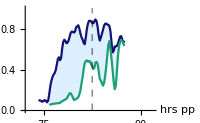
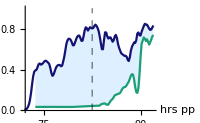
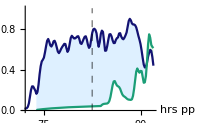
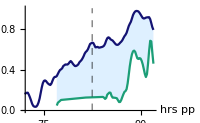
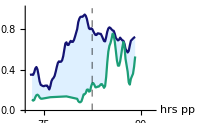

```mathematica
Row@plotFn[agg25t~Join~agg26t~Join~agg28t~Join~agg29~Join~agg30t,secondharmonic,"filter"-> 3,"join"->True,"rescale"-> True]
```

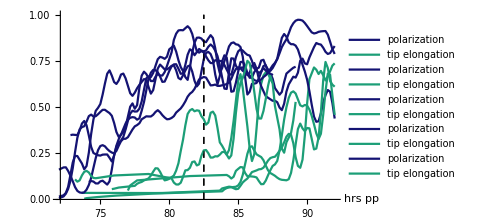

```mathematica
Show@plotFn[agg25t~Join~agg26t~Join~agg28t~Join~agg29~Join~agg30t,secondharmonic,
"filter"-> 3,"join"->True,"filling"-> None,"imgsize"-> Medium]
```

```mathematica
(* four raw datasets *)
```

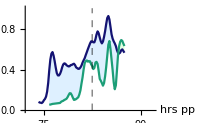
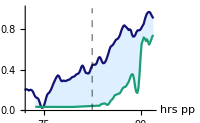
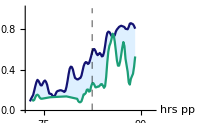
-Graphics--Graphics--Graphics--Graphics-

```mathematica
Row@plotFn[agg25~Join~agg26~Join~agg29~Join~agg30,Delete[secondharmonic,3],"filter"-> 3,"join"->True ]
```

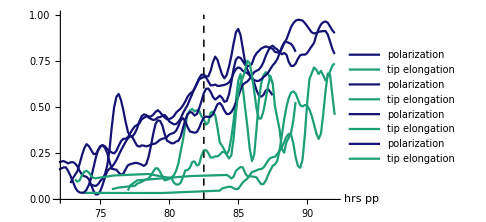

```mathematica
Show@plotFn[agg25~Join~agg26~Join~agg29~Join~agg30,Delete[secondharmonic,3],"filter"-> 3,"join"->True,
"filling"-> None,"imgsize"-> Medium]
```

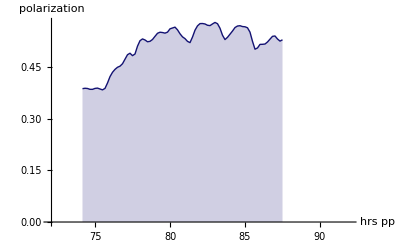
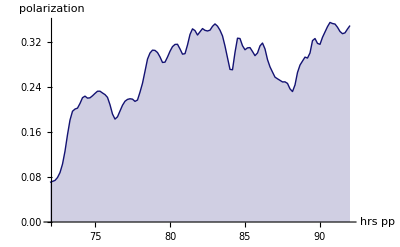
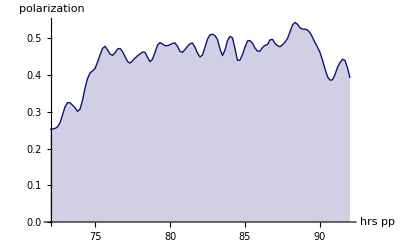
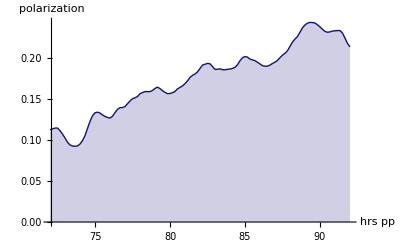
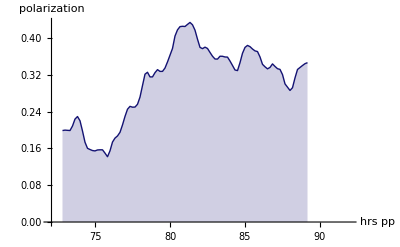
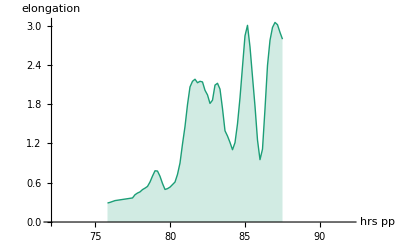
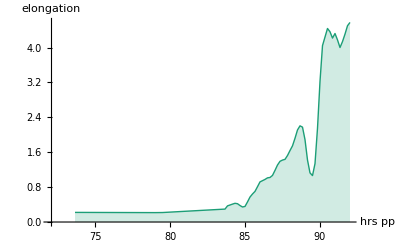
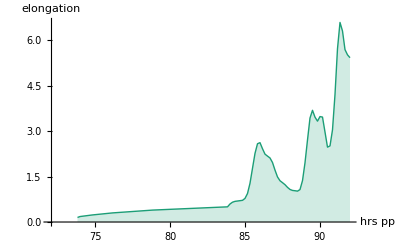

```mathematica
{pol,elong}=Transpose[plotFn[agg25t~Join~agg26t~Join~agg28t~Join~agg29~Join~agg30t,secondharmonic,
"filter"-> 3,"join"->True,"rescale"->False],{2,1}]

Row@{Show[pol,PlotRange-> {{72,92},{0,0.56}},ImageSize-> Medium],Show[elong,PlotRange-> {{72,92},{0,6.2}},ImageSize-> Medium]}
```